# Easy Application

#### Graph Paraboloid

```mathematica
paraboloid=ContourPlot3D[x^2+y^2==z,{x,-5,5},{y,-5,5},{z,0,18},PlotRange->{0,18},ContourStyle->Opacity[0.5,Blue],Mesh->None,RegionFunction->Function[{x,y,z},z<1500000],Lighting->"Neutral"];
```

```mathematica
Show[paraboloid,Boxed->False]
```

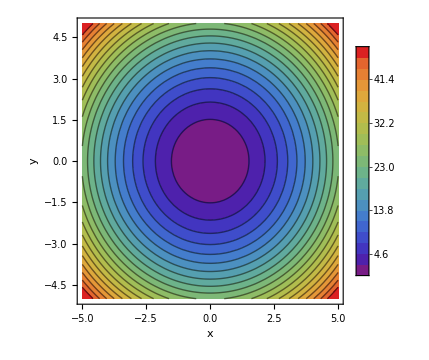

```mathematica
ContourPlot[x^2+y^2,{x,-5,5},{y,-5,5},Contours->20,ColorFunction->"Rainbow",PlotLegends->Automatic,FrameLabel->{"x","y"},ImageSize->Medium]
```

#### Descent with Learning Rate 15

```mathematica
(*100 steps, learning rate 15*)
file1= FileNameJoin[{NotebookDirectory[],"points1.txt"}];
points1=Import[file1,"Table"];
paraboloid=ContourPlot3D[x^2+y^2==z,{x,-1300,1300},{y,-1300,1300},{z,0,1500000},PlotRange->{0,1500000},ContourStyle->Opacity[0.5,Blue],Mesh->None,RegionFunction->Function[{x,y,z},z<1500000],Lighting->"Neutral"];

startingPoint=Graphics3D[{Opacity[1],Black,Ellipsoid[{640.32,832.27,(640.32^2+832.27^2)},{40,40,25000}]}];
endingPoint=Graphics3D[{Opacity[1],Blue,Ellipsoid[{0, 0, 0},{40,40,25000}]}];otherPoints1=Graphics3D[Table[{Opacity[0.5],Black,Ellipsoid[point,{20,20,12000}]},{point,points1}]];

Show[{paraboloid,startingPoint,otherPoints1,endingPoint},PlotRange->All,Boxed->False,ImageSize->Full]
```

-Graphics3D-

#### Descent with Learning Rate 100

```mathematica
(*100 steps, learning rate 100*)
file2 = FileNameJoin[{NotebookDirectory[],"points2.txt"}];
points2=Import[file2,"Table"];
```

```mathematica
otherPoints2=Graphics3D[Table[{Opacity[0.5],Black,Ellipsoid[point,{20,20,12000}]},{point,points2}]];

Show[{paraboloid,startingPoint,otherPoints2,endingPoint},PlotRange->All,Boxed->False,ImageSize->Full]
```

-Graphics3D-

#### Descent with Learning Rate 5

```mathematica
(*100 steps, learning rate 5*)
```

```mathematica
file3 = FileNameJoin[{NotebookDirectory[],"points3.txt"}];
points3=Import[file3,"Table"];
```

```mathematica
otherPoints3=Graphics3D[Table[{Opacity[0.5],Black,Ellipsoid[point,{20,20,12000}]},{point,points3}]];

Show[{paraboloid,startingPoint,otherPoints3,endingPoint},PlotRange->All,Boxed->False,ImageSize->Full]
```

-Graphics3D-